```mathematica
bit[n_,k_]:=Mod[Floor[n/2^k],2];
bits[n_,depth_:5]:=Reverse@Table[bit[n,k],{k,0,depth}]
bbits[n_,depth_:5]:=StringJoin@@(ToString/@bits[n,depth])
```

```mathematica
Hexagon[{x_,y_},r_]:=Line[Table[
r{Sin[2Pi/6 k],Cos[2Pi/6k]}+{x,y},{k,0,6}]]
```

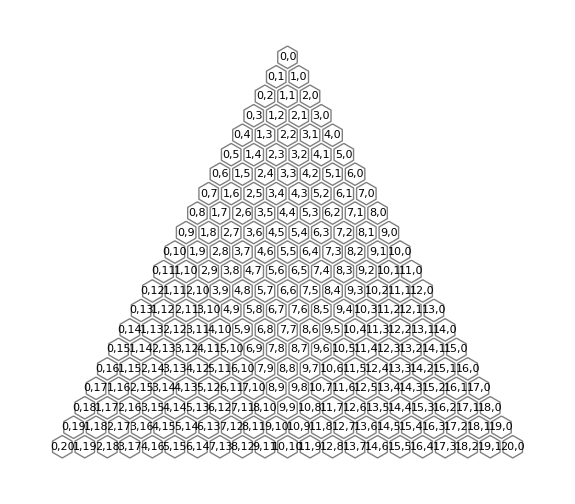

```mathematica
rows = 20;Graphics[Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
GrayLevel[.5],Thin,
Hexagon[location,1],Black,Text[ToString[i]<>","<>ToString[j],location]},{i,0,rows},{j,0,rows-i}]]
```

```mathematica
rows = 5;Graphics[Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
GrayLevel[.5],Thin,
Hexagon[location,1],Black,Text[Style[
ToString[i+j]<>"\n"<>
ToString[i]<>"  "<>ToString[j],"Centered"],location]},{i,0,rows},{j,0,rows-i}]]
```

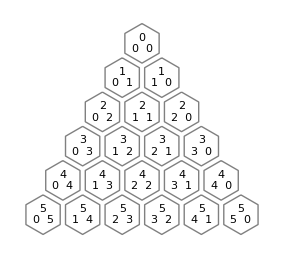

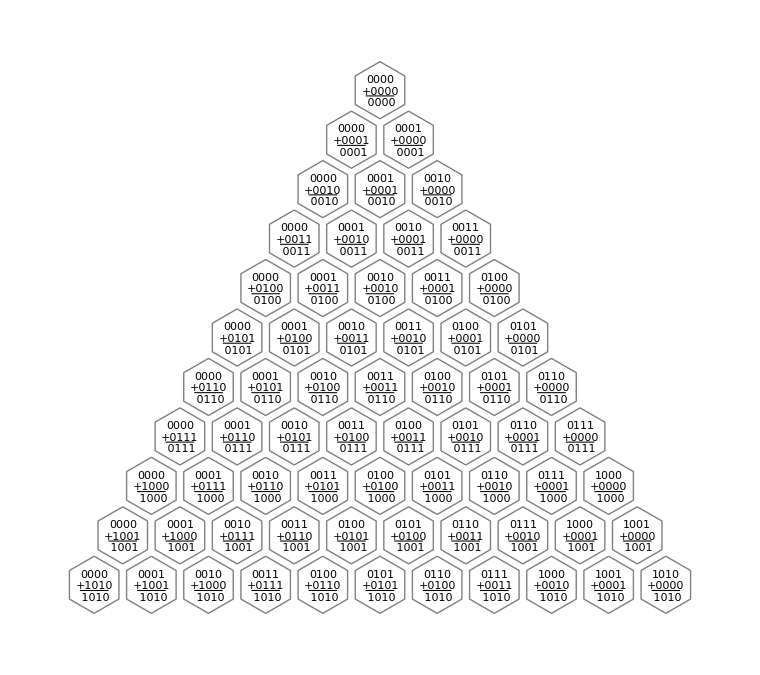

```mathematica
rows = 10;Graphics[Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
GrayLevel[.5],Thin,
Hexagon[location,1],
Black,Thickness[.001],
Line[(#+location)&/@{{-.5,-.2},{.5,-.2}}],
Text[Style[
" "<>bbits[i,3]<>"\n+"<>bbits[j,3]<>"\n "<>bbits[i+j,3],"Centered",FontFamily->"Courier"],location+{0,-.05}]},{i,0,rows},{j,0,rows-i}]]
```

```mathematica
3
```

```mathematica
4
```

```mathematica
rows = 10;Graphics[Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
GrayLevel[.5],Thin,
Hexagon[location,1],Black,Text[Style[
ToString[i+j]<>"\n"<>
ToString[i]<>"  "<>ToString[j],"Centered"],location]},{i,0,rows},{j,0,rows-i}]]
```

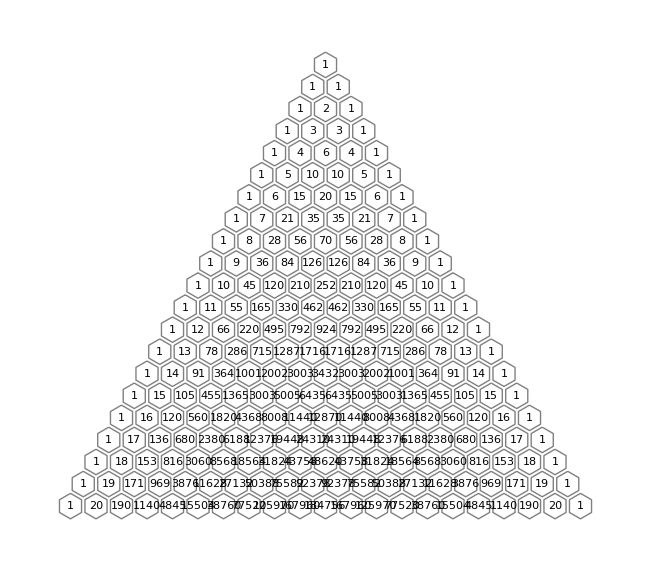

```mathematica
rows = 20;Graphics[Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
GrayLevel[.5],Thin,
Hexagon[location,1],Black,Text[ToString[Binomial[i+j,i]],location]},{i,0,rows},{j,0,rows-i}]]
```

```mathematica
rows = 10;position =2;
Graphics[
{Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
GrayLevel[.25],Thin,
Line@@ Hexagon[location,1]},{i,0,rows},{j,0,rows-i}],
Table[ {GrayLevel[.26],

Line[{(0+1){-1,-√3}+(i+1){1,-√3}+{1.5,0},(i+2){0,-√3}+{24,0}-{1.5,0}}],
Text[bbits[i,3],(i+2){0,-√3}+{24,0}]}
,{i,0,rows}],
Table[ {GrayLevel[.26],Rotate[
Text[bbits[i],(i){-1,-√3}+{-1.7,-.2}],-Pi/3]}
,{i,0,rows}]


}]
```

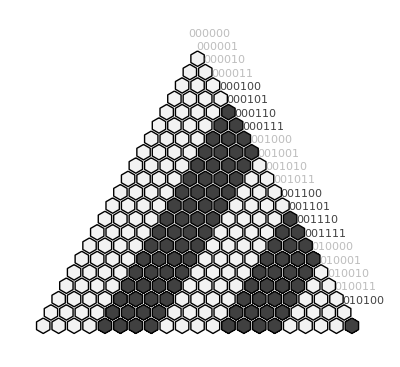

```mathematica
rows = 20;
position = 2;
Graphics[
{Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
If[bit[i,position]==0,GrayLevel[.95],GrayLevel[.25]],Thin,
Polygon@@ Hexagon[location,1],Black,Hexagon[location,1]},{i,0,rows},{j,0,rows-i}],
Table[ {
If[bit[i,position]==0,GrayLevel[.74],GrayLevel[.26]],Rotate[
Text[bbits[i],(i){1,-√3}+{1.5,-.2}],Pi/3]}
,{i,0,rows}]}]
```

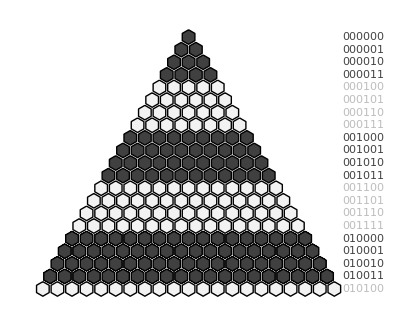

```mathematica
rows = 20;position =2;
Graphics[
{Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
If[bit[i+j,position]==1,GrayLevel[.95],GrayLevel[.25]],Thin,
Polygon@@ Hexagon[location,1],Black,Hexagon[location,1]},{i,0,rows},{j,0,rows-i}],
Table[ {If[bit[i,position]==1,GrayLevel[.74],GrayLevel[.26]],
Text[bbits[i],(i+2){0,-√3}+{24,0}]}
,{i,0,rows}]}]
```

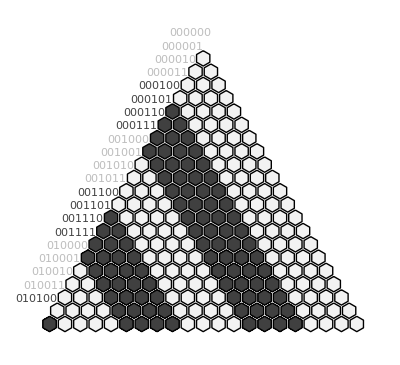

```mathematica
rows = 20;position= 2;
Graphics[
{Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
If[bit[j,position]==0,GrayLevel[.95],GrayLevel[.25]],Thin,
Polygon@@ Hexagon[location,1],Black,Hexagon[location,1]},{i,0,rows},{j,0,rows-i}],
Table[ {If[bit[i,position]==0,GrayLevel[.74],GrayLevel[.26]],Rotate[
Text[bbits[i],(i){-1,-√3}+{-1.7,-.2}],-Pi/3]}
,{i,0,rows}]}]
```

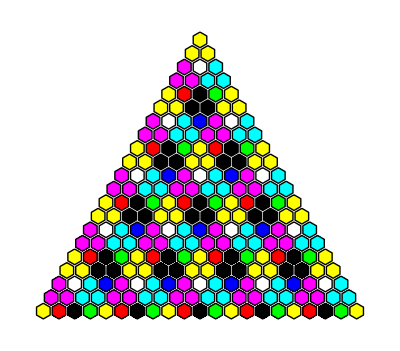

```mathematica
rows = 20;position=1;
Graphics[
{Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
cc={0,0,0};
If[bit[i,position]==0,cc=cc+{1,0,0}];
If[bit[j,position]==0,cc=cc+{0,1,0}];
If[bit[i+j,position]==1,cc=cc+{0,0,1}];RGBColor@@(cc),Thin,
Polygon@@ Hexagon[location,1],Black,{If[bit[i,position]==0 && bit[j,position]==0&& bit[i+j,position]==1
,Thick],
Hexagon[location,1]}},{i,0,rows},{j,0,rows-i}]}]
```

```mathematica
rows = 33;
GraphicsGrid[{Table[Graphics[
{Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
If[bit[i,pp]==0&&bit[j,pp]==0&&bit[i+j,pp]==1, GrayLevel[.95],GrayLevel[.25]],Thin,
Polygon@@ Hexagon[location,1],Black,Hexagon[location,1]},{i,0,rows},{j,0,rows-i}]}],{pp,1,3}]}]
```

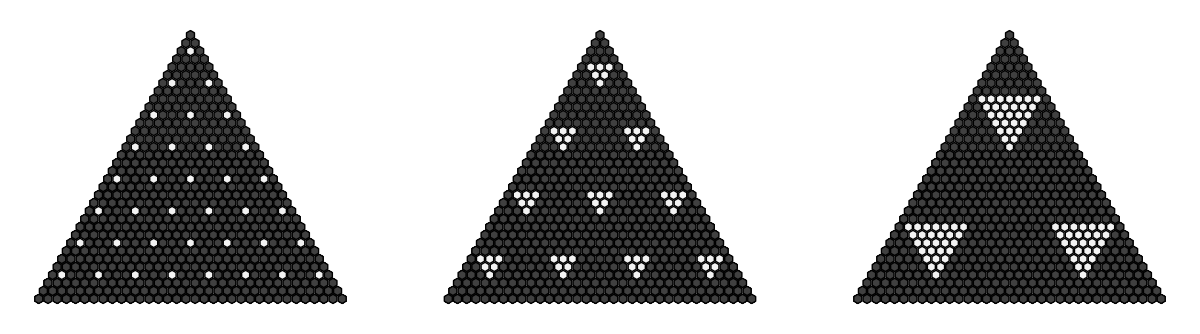

```mathematica
rows = 33;
GraphicsGrid[{Table[Graphics[
{Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
If[bit[i,pp]==0&&bit[j,pp]==0&&bit[i+j,pp]==1, GrayLevel[.95],GrayLevel[.25]],Thin,
Polygon@@ Hexagon[location,1],Black,Hexagon[location,1]},{i,0,rows},{j,0,rows-i}]}],{pp,1,3}]}]
```

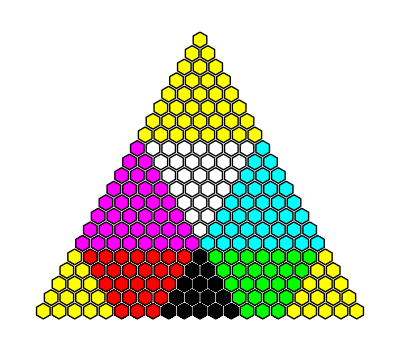

```mathematica
rows = 20;position=3;
Graphics[
{Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
cc={0,0,0};
If[bit[i,position]==0,cc=cc+{1,0,0}];
If[bit[j,position]==0,cc=cc+{0,1,0}];
If[bit[i+j,position]==1,cc=cc+{0,0,1}];RGBColor@@(cc),Thin,
Polygon@@ Hexagon[location,1],Black,Hexagon[location,1]},{i,0,rows},{j,0,rows-i}]}]
```

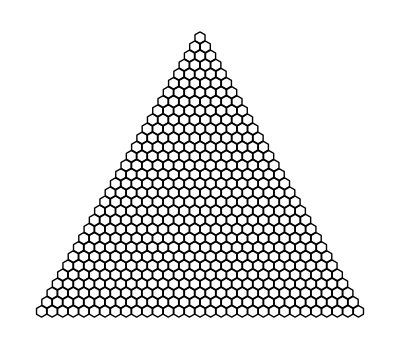

```mathematica
rows = 30;Graphics[
{Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{Thin,Black,Hexagon[location,1.1]},{i,0,rows},{j,0,rows-i}]}]
```

```mathematica
2
```

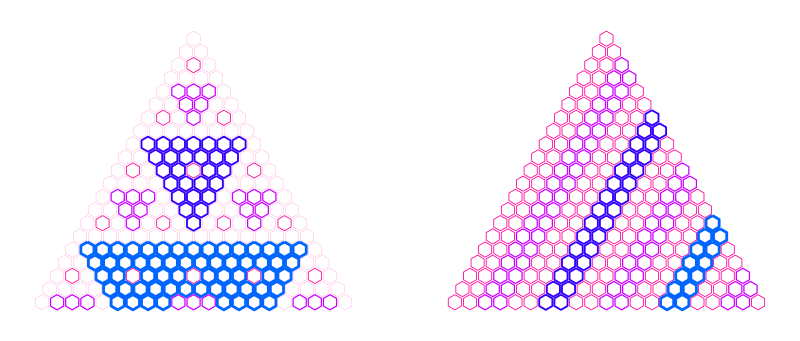

```mathematica
rows = 20;
GraphicsGrid[{{Graphics[
{Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
bb=1;cc=.000001;bbb=1; Table[If[bit[i,bb]==0 && bit[j,bb]==0&& bit[i+j,bb]==1,bbb=bb;cc=.001*1.5^bb],{bb,Floor[Log[2,rows]],1,-1}]; Thickness[cc],Hue[1-bbb/10],
Hexagon[location,1]},{i,0,rows},{j,0,rows-i}]}],
Graphics[
{Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
bb=1;cc=.000001;bbb=1; Table[If[bit[i,bb]==0 ,bbb=bb;cc=.001*1.5^bb],{bb,Floor[Log[2,rows]],1,-1}]; Thickness[cc],Hue[1-bbb/10],
Hexagon[location,1]},{i,0,rows},{j,0,rows-i}]}]}}]
```

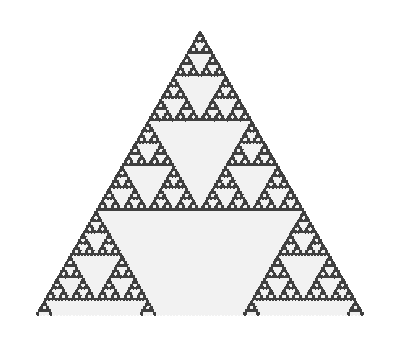

```mathematica
rows = 100;
base = 2;
Graphics[Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
If[Mod[Binomial[i+j,i],base]==0,GrayLevel[.95],GrayLevel[.25]],Thin,
Polygon@@ Hexagon[location,1],Black},{i,0,rows},{j,0,rows-i}]]
```

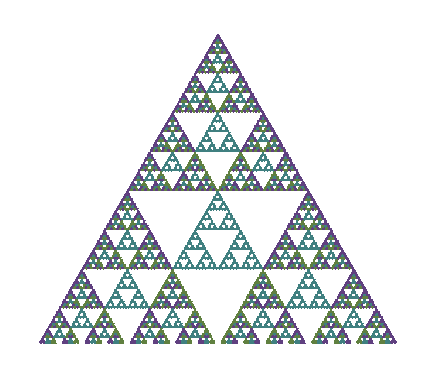

```mathematica
rows = 125;
base = 4;
Graphics[Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
If[(ss=Mod[Binomial[i+j,i],base])==0,GrayLevel[1],
Hue[1-Mod[Binomial[i+j,i],base]/base,.5,.5]],Thin,
Polygon@@ Hexagon[location,1],Black},{i,0,rows},{j,0,rows-i}]]
```

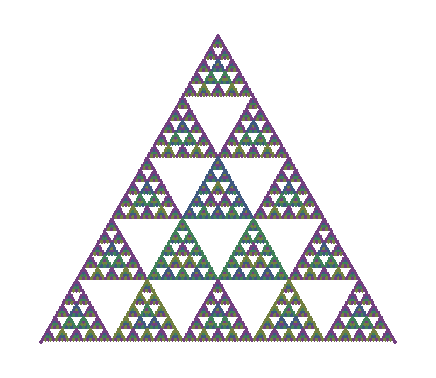

```mathematica
rows = 125;
base = 5;
Graphics[Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
If[(ss=Mod[Binomial[i+j,i],base])!=0,
{Hue[1-Mod[Binomial[i+j,i],base]/base,.5,.5],
Polygon@@ Hexagon[location,1]}]},{i,0,rows},{j,0,rows-i}]]
```

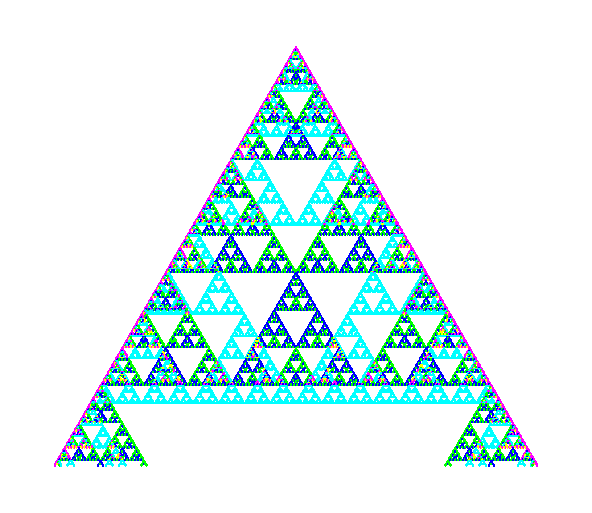

```mathematica
rows = 300;
base = 6;
Graphics[Table[
location = (i+1){1,-√3}+(j+1){-1,-√3};
{
If[(ss=Mod[Binomial[i+j,i],base])!=0,
{Hue[1-Mod[Binomial[i+j,i],base]/base],
Polygon@@ Hexagon[location,1]}]},{i,0,rows},{j,0,rows-i}]]
```